```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-up-xi1-baryon.wdx"];
Hdg1=Query[1,1]@gpd;
Hdg2=Query[1,2]@gpd;
Her=Query[1,3]@gpd;
Hda=Query[1,4]@gpd;
Edg1=Query[2,1]@gpd;
Edg2=Query[2,2]@gpd;
Eer=Query[2,3]@gpd;
Eda=Query[2,4]@gpd;
Hdgf1=Interpolation[Flatten[Hdg1,1]];
Hdgf2=Interpolation[Flatten[Hdg2,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf1=Interpolation[Flatten[Edg1,1]];
Edgf2=Interpolation[Flatten[Edg2,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
gpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-up-xi1-baryon.wdx"];
Hdg1=Query[1,1]@gpdd;
Hdg2=Query[1,2]@gpdd;
Her=Query[1,3]@gpdd;
Hda=Query[1,4]@gpdd;
Edg1=Query[2,1]@gpdd;
Edg2=Query[2,2]@gpdd;
Eer=Query[2,3]@gpdd;
Eda=Query[2,4]@gpdd;
Hdgf1=Interpolation[Flatten[Hdg1,1]];
Hdgf2=Interpolation[Flatten[Hdg2,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf1=Interpolation[Flatten[Edg1,1]];
Edgf2=Interpolation[Flatten[Edg2,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t];
```

```mathematica
(*Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];*)
```

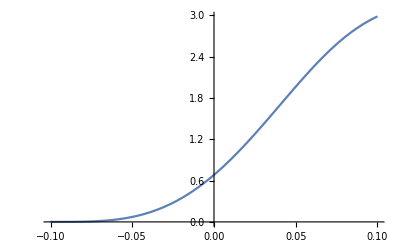

```mathematica
Plot[-I*Herf[x,-1],{x,-0.1,0.1}]
```

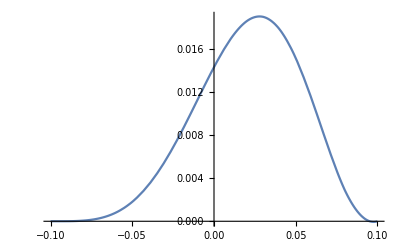

```mathematica
Plot[-I*Hdaf[x,-1],{x,-0.1,0.1}]
```

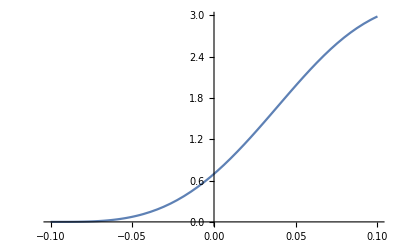

```mathematica
Plot[-I*Herall[x,-1],{x,-0.1,0.1}]
```

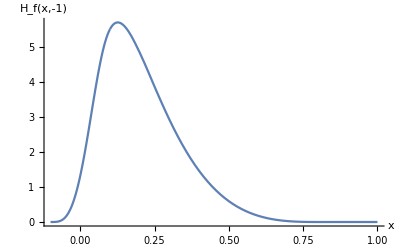

```mathematica
pHf2d=Show[Plot[I*Hdgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[I*Hdgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_f(x,-1)"}]
```

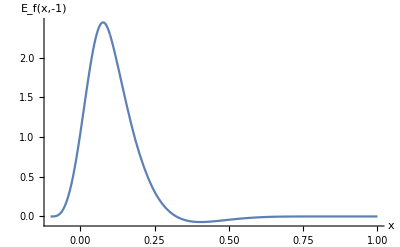

```mathematica
pEf2d=Show[Plot[I*Edgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[I*Edgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_f(x,-1)"}]
```

```mathematica
pHf3d=Show[Plot3D[I*Hdgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Hdgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_f(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEf3d=Show[Plot3D[I*Edgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Edgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_f(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[-I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-

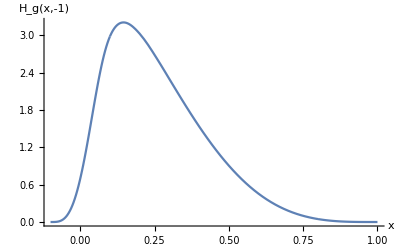

```mathematica
pHg2d=Show[Plot[-I*Hdgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[-I*Hdgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[-I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_g(x,-1)"}]
```

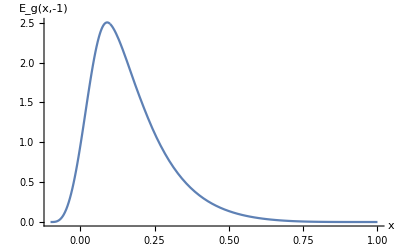

```mathematica
pEg2d=Show[Plot[-I*Edgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[-I*Edgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[-I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_g(x,-1)"}]
```

```mathematica
pHg3d=Show[Plot3D[-I*Hdgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Hdgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_g(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEg3d=Show[Plot3D[-I*Edgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Edgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_g(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
fpathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Hu-0.1-baryon.pdf"}];
fpathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Eu-0.1-baryon.pdf"}];
```

```mathematica
fpathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Hu-0.1-2d-baryon.pdf"}];
fpathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Eu-0.1-2d-baryon.pdf"}];
```

```mathematica
gpathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Hu-0.1-baryon.pdf"}];
gpathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Hu-0.1-2d-baryon.pdf"}];
gpathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Eu-0.1-baryon.pdf"}];
gpathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Eu-0.1-2d-baryon.pdf"}];
```

```mathematica
Export[gpathH3d,pHg3d]
Export[gpathH,pHg2d]
Export[gpathE3d,pEg3d]
Export[gpathE,pEg2d]
```

G:\calc-online\gpd\3dre\228test\g-Hu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\g-Hu-0.1-2d-baryon.pdf

G:\calc-online\gpd\3dre\228test\g-Eu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\g-Eu-0.1-2d-baryon.pdf

```mathematica
Export[fpathH3d,pHf3d]
Export[fpathH,pHf2d]
Export[fpathE3d,pEf3d]
Export[fpathE,pEf2d]
```

G:\calc-online\gpd\3dre\228test\f-Hu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\f-Hu-0.1-2d-baryon.pdf

G:\calc-online\gpd\3dre\228test\f-Eu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\f-Eu-0.1-2d-baryon.pdf

```mathematica
SubscriptBox["H",e]//DisplayForm
```

H_e

```mathematica
Plot3D[Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[-I*Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

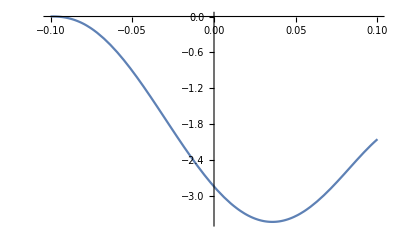

```mathematica
Plot[-I*Chop[Eerf[x,-0.1],10^-9],{x,-0.1,0.1}]
```

```mathematica
Eerf[0,-0.1]
```

0.-2.83547 ⅈ

```mathematica
Eerf[0.02,-0.1]
```

-8.32662×10^-26-3.30567 ⅈ

```mathematica
Eerf[-0.005,-0.1]
```

-1.49999×10^-11-2.67216 ⅈ

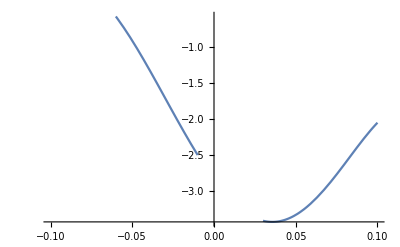

```mathematica
Plot[-I*Eerf[x,-0.1],{x,-0.1,0.1}]
```

```mathematica
Plot3D[I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-